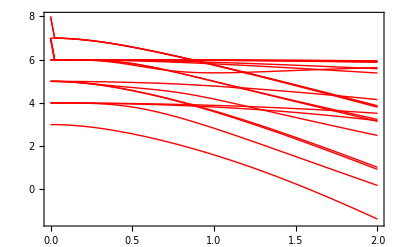

```mathematica
(*NMax=6 *)
(*Data3=Table[Data[i],{i,1,nEigValues}];*)
ListPlot[Data3,Joined->True,PlotRange->{{α0Min,α0Max},{-1.5,8}},Frame->True,PlotStyle->{Red}]
```

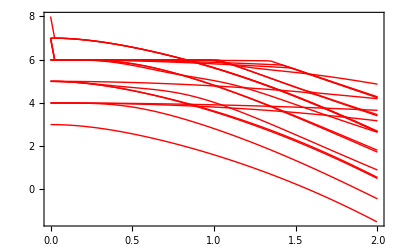

```mathematica
(*NMax=10 *)
(*Data4=Table[Data[i],{i,1,nEigValues}];*)
ListPlot[Data4,Joined->True,PlotRange->{{α0Min,α0Max},{-1.5,8}},Frame->True,PlotStyle->{Red}]
```

```mathematica
(*NMax=14 *)
Data5=Table[Data[i],{i,1,nEigValues}];
ListPlot[Data5,Joined->True,PlotRange->{{α0Min,α0Max},{-1.5,8}},Frame->True,PlotStyle->{Red}]
```

-Graphics-

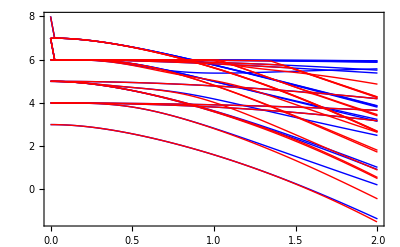

```mathematica
Show[ListPlot[Data3,Joined->True,PlotRange->{{α0Min,α0Max},{-1.5,8}},Frame->True,PlotStyle->Directive[Blue,Medium]],ListPlot[Data4,Joined->True,PlotRange->{{α0Min,α0Max},{-1.5,8}},Frame->True,PlotStyle->Directive[Black,Medium]],
ListPlot[Data4,Joined->True,PlotRange->{{α0Min,α0Max},{-1.5,8}},Frame->True,PlotStyle->Directive[Red,Medium]]]
```